```mathematica
ClearAll["Global`*"]
```

## Cd116

```mathematica
enBMCd={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
strBMCd={0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000002,0.0000000008,0.0000000032,0.0000000131,0.0000000500,0.0000001806,0.0000006175,0.0000019979,0.0000061157,0.0000177110,0.0000485267,0.0001257945,0.0003085295,0.0007159761,0.0015721154,0.0032664647,0.0064226064,0.0119516638,0.0210518143,0.0351057435,0.0554383289,0.0829368340,0.1176030713,0.1581789586,0.2020242066,0.2453889510,0.2841038882,0.3145410580,0.3345545862,0.3440711336,0.3451007154,0.3411465722,0.3362174097,0.3337854571,0.3360294430,0.3435612908,0.3556275791,0.3705956289,0.3864576599,0.4011442732,0.4125970558,0.4187249224,0.4174643033,0.4071259935,0.3870659892,0.3585555516,0.3256458286,0.2958579627,0.2806162928,0.2953578964,0.3591130221,0.4931078517,0.7177990792,1.0479803023,1.4863568545,2.0171173602,2.6020237421,3.1816999929,3.6836378654,4.0360914175,4.1843924895,4.1045873801,3.8096783531,3.3462097858,2.7824323821,2.1922043282,1.6398549785,1.1701519473,0.8050441600,0.5462903971,0.3814957341,0.2908433727,0.2526067049,0.2466915098,0.2563969920,0.2690171409,0.2758748464,0.2721166209,0.2563342859,0.2299611832,0.1964269168,0.1601688473,0.1256890879,0.0968463787,0.0764801712,0.0663310091,0.0671178999,0.0786115667,0.0996102920,0.1278450065,0.1599476391,0.1916497975,0.2183095481,0.2357163116,0.2409675731,0.2331297922,0.2134415452,0.1849776547,0.1518958472,0.1185370964,0.0886813266,0.0651670465,0.0499185946,0.0442622830,0.0493123220,0.0661950943,0.0959519302,0.1390933207,0.1949361695,0.2609911779,0.3327211988,0.4039168617,0.4677325359,0.5181613891,0.5515211999,0.5674820551,0.5693241684,0.5633926265,0.5579720674,0.5619142989,0.5832887095,0.6281711203,0.6995724094,0.7965234800,0.9134667632,1.0402513459,1.1630548844,1.2663799197,1.3359211046,1.3617040311,1.3406355339,1.2776253927,1.1847806307,1.0787434256,0.9768455822,0.8931614647,0.8355939303,0.8047915993,0.7950874842,0.7969926416,0.8003175171,0.7968919043,0.7821287038,0.7551915197,0.7180553734,0.6740781694,0.6267190173,0.5787893131,0.5322654633,0.4884216425,0.4479792155,0.4111076332,0.3773272103,0.3455048184,0.3141142740,0.2817857523,0.2480121719,0.2138379148,0.1824705230,0.1599638701,0.1562780483,0.1869708299,0.2754180800,0.4548106693,0.7684141634,1.2660785739,1.9952555786,2.9862427233,4.2340068360,5.6819575243,7.2149331238,8.6677955170,9.8516979751,10.5933682490,10.7764489400,10.3713487979,9.4430554051,8.1340626229,6.6285757499,5.1103541842,3.7273579340,2.5720252611,1.6791558646,1.0373237602,0.6067242195,0.3366968305,0.1786637042,0.0931850547,0.0520077121,0.0369289850,0.0372492498,0.0470463657,0.0629132824,0.0823817727,0.1030370881,0.1222352831,0.1372834798,0.1458942368,0.1466888613,0.1395338247,0.1255685850,0.1069056145,0.0861068572,0.0656134075,0.0473004263,0.0322593134,0.0208143467,0.0127053915,0.0073372095,0.0040085877,0.0020719032,0.0010131299};
enBPCd={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
strBPCd={0.0000000000,0.0000000001,0.0000000003,0.0000000010,0.0000000032,0.0000000090,0.0000000244,0.0000000624,0.0000001510,0.0000003461,0.0000007509,0.0000015430,0.0000030046,0.0000055474,0.0000097206,0.0000161865,0.0000256590,0.0000388121,0.0000561894,0.0000781484,0.0001048683,0.0001364003,0.0001726970,0.0002135251,0.0002582051,0.0003052246,0.0003519011,0.0003943433,0.0004279007,0.0004480960,0.0004517833,0.0004381060,0.0004088539,0.0003680493,0.0003209117,0.0002726005,0.0002271862,0.0001871445,0.0001534107,0.0001258089,0.0001035808,0.0000857999,0.0000715852,0.0000601543,0.0000508105,0.0000429406,0.0000360480,0.0000297976,0.0000240372,0.0000187735,0.0000141101,0.0000101771,0.0000070881,0.0000049584,0.0000040221,0.0000049039,0.0000091469,0.0000201513,0.0000447047,0.0000952184,0.0001925296,0.0003686362,0.0006680425,0.0011457625,0.0018599447,0.0028580621,0.0041579347,0.0057280303,0.0074742107,0.0092405472,0.0108287504,0.0120344793,0.0126916342,0.0127111400,0.0121013935,0.0109636992,0.0094650161,0.0077980353,0.0061416829,0.0046328105,0.0033539921,0.0023361328,0.0015705822,0.0010245134,0.0006547726,0.0004177819,0.0002751643,0.0001959760,0.0001568005,0.0001408059,0.0001365082,0.0001366277,0.0001371584,0.0001366072,0.0001352933,0.0001346178,0.0001362804,0.0001415188,0.0001505128,0.0001621129,0.0001739889,0.0001831748,0.0001868524,0.0001831227,0.0001715171,0.0001530908,0.0001300953,0.0001053704,0.0000816756,0.0000611652,0.0000451291,0.0000340081,0.0000276044,0.0000253684,0.0000266488,0.0000308360,0.0000373777,0.0000456971,0.0000550739,0.0000645656,0.0000730287,0.0000792605,0.0000822320,0.0000813331,0.0000765406,0.0000684395,0.0000580868,0.0000467616,0.0000356875,0.0000258102,0.0000176844,0.0000114767,0.0000070535,0.0000041048,0.0000022616,0.0000011797,0.0000005825,0.0000002723,0.0000001204,0.0000000504,0.0000000200,0.0000000075,0.0000000027,0.0000000009,0.0000000003,0.0000000001,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000};
```

## Sn116

```mathematica
enBPSn={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
strBPSn={0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000001,0.0000000004,0.0000000014,0.0000000051,0.0000000175,0.0000000566,0.0000001733,0.0000005017,0.0000013746,0.0000035629,0.0000087373,0.0000202718,0.0000445005,0.0000924303,0.0001816627,0.0003378785,0.0005947879,0.0009912218,0.0015643986,0.0023396608,0.0033190525,0.0044733344,0.0057431305,0.0070535554,0.0083422872,0.0095945462,0.0108722512,0.0123220139,0.0141501291,0.0165627650,0.0196836468,0.0234745587,0.0276898182,0.0318898468,0.0355207437,0.0380418907,0.0390623500,0.0384397115,0.0363071746,0.0330217680,0.0290565365,0.0248783888,0.0208531401,0.0172021718,0.0140111677,0.0112724470,0.0089356395,0.0069466639,0.0052664689,0.0038719068,0.0027470197,0.0018732930,0.0012241347,0.0007647869,0.0004560603,0.0002593226,0.0001406538,0.0000731704,0.0000375241,0.0000211570,0.0000170188,0.0000222938,0.0000374019,0.0000652858,0.0001108059,0.0001799883,0.0002788968,0.0004120401,0.0005804616,0.0007799289,0.0009998507,0.0012235719,0.0014304590,0.0015996892,0.0017150332,0.0017694044,0.0017677718,0.0017273592,0.0016748313,0.0016411585,0.0016556861,0.0017412146,0.0019114290,0.0021708945,0.0025165397,0.0029387681,0.0034206444,0.0039350693,0.0044417939,0.0048873787,0.0052107298,0.0053545168,0.0052796315,0.0049776258,0.0044762109,0.0038355904,0.0031373804,0.0024711738,0.0019248192,0.0015827947,0.0015334492,0.0018818288,0.0027617614,0.0043399299,0.0068063875,0.0103502070,0.0151244719,0.0212092524,0.0285818906,0.0370997347,0.0464935593,0.0563653930,0.0661872539,0.0753075108,0.0829824447,0.0884516481,0.0910607786,0.0904083191,0.0864692343,0.0796441922,0.0707048213,0.0606442689,0.0504786167,0.0410606551,0.0329573420,0.0264140837,0.0213979235,0.0176905675,0.0149957616,0.0130311908,0.0115869214,0.0105451628,0.0098667208,0.0095565431,0.0096236074,0.0100489604,0.0107706876,0.0116876296,0.0126771231,0.0136180896,0.0144106324,0.0149865937,0.0153104991,0.0153744811,0.0151921033,0.0147941028,0.0142254968,0.0135409443,0.0127957599,0.0120334573,0.0112747865,0.0105149541,0.0097336943,0.0089186543,0.0080999039,0.0073958222,0.0070788114,0.0076795147,0.0101524736,0.0161139611,0.0281248937,0.0499268000,0.0864619038,0.1434575141,0.2263862723,0.3387766502,0.4801424645,0.6441391457,0.8177674822,0.9823476454,1.1164964370,1.2005800783,1.2214014706,1.1755873015,1.0704791605,0.9222048495,0.7516266449,0.5795658501,0.4227953089,0.2918008705,0.1905368275,0.1177146878,0.0688219136,0.0381049520,0.0200336471,0.0101002849,0.0050535511,0.0027755720,0.0020044045,0.0020415504,0.0025142496,0.0032119180,0.0039898782,0.0047245598,0.0053035666,0.0056354717,0.0056659644,0.0053895446,0.0048501198,0.0041292548,0.0033258973,0.0025343329,0.0018269898,0.0012460234,0.0008039589,0.0004907486,0.0002834014,0.0001548326,0.0000800277,0.0000391324};
```

## Figure 1

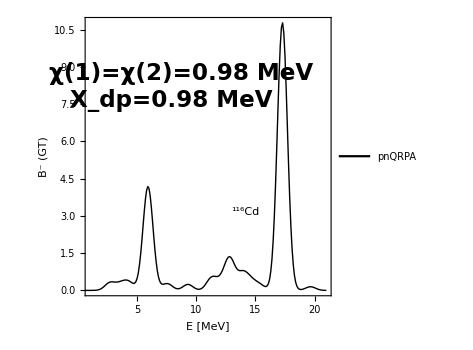

```mathematica
tableFig1=Table[{enBMCd[[i]],strBMCd[[i]]},{i,1,Length[strBMCd]}];
fig1=ListPlot[tableFig1,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{1,21},Full},FrameLabel->{"E [MeV]","B^- (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.35,0.9}],Epilog->{Inset[Style["χ(1)=χ(2)=0.98 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.39,0.8}]],Inset[Style["X_dp=0.98 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.7}]],Inset[Framed[Style[Row[{Superscript["","116"],"Cd"}],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.65,0.3}]]}];
Show[fig1]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_5/new_figs/fig1_set5.pdf",Show[fig1],ImageResolution->1200];
```

## Figure 2

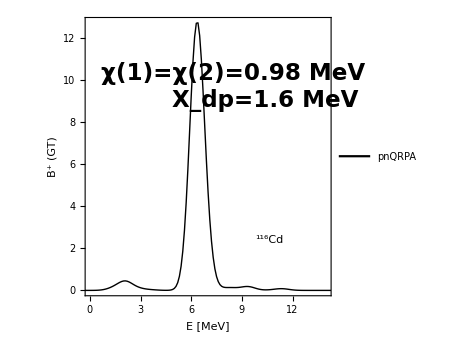

```mathematica
tableFig2=Table[{enBPCd[[i]],strBPCd[[i]]*1000},{i,1,Length[strBPCd]}];
fig2=ListPlot[tableFig2,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{0,14},Full},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.7,0.9}],Epilog->{Inset[Style["χ(1)=χ(2)=0.98 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.6,0.8}]],Inset[Style["X_dp=1.6 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.73,0.7}]],Inset[Framed[Style[Row[{Superscript["","116"],"Cd"}],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.75,0.2}]]}];
Show[fig2]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_5/new_figs/fig2_set5.pdf",Show[fig2],ImageResolution->1200];
```

## Figure 3

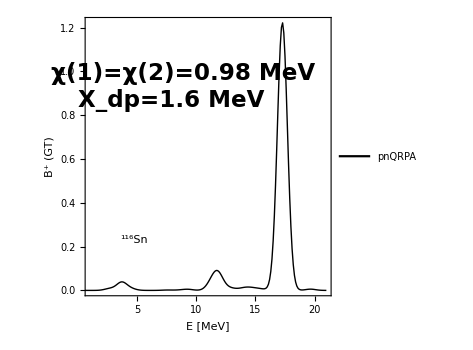

```mathematica
tableFig3=Table[{enBPSn[[i]],strBPSn[[i]]},{i,1,Length[strBPSn]}];
fig3=ListPlot[tableFig3,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{1,21},Full},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.35,0.9}],Epilog->{Inset[Style["χ(1)=χ(2)=0.98 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.4,0.8}]],Inset[Style["X_dp=1.6 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.7}]],Inset[Framed[Style[Row[{Superscript["","116"],"Sn"}],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.2,0.2}]]}];
Show[fig3]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_5/new_figs/fig3_set5.pdf",Show[fig3],ImageResolution->1200];
```